# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most conlang lexicons are generated manually or through the help of random combination algorithms, I present several algorithms and metrics for computationally generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages. In the end, I present a vocabulary of “average” words derived from the Swadesh word list.

## Introduction

A conlang’s lexicon can offer crucial information about the purpose and intended speakers of the conlang. The conlang Esperanto was created in 1887, aiming to create a “universal” language that could be learned and spoken by anyone with relative ease. However, Esperanto’s lexicon was heavily biased towards Romance and Germanic languages, undermining its original purpose of being universal. This research uses genetic algorithms and neural networks to attempt to quantify universality and generate a lexicon that is the optimal “average” of the world languages.

## Initial Setup

In order to derive average words, I needed a large corpus of multilingual words. I used the built-in database of languages in the Wolfram Language.

Get the top 100 most spoken languages:

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
Iconize[languages, "List of languages"]
```

Get raw translations of our keyWord to the determined languages:

```mathematica
keyWord = "sun";
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[keyWord, languages]];
rawTranslations//Short
```

{Chinese→太陽,English→sun,Mandarin Chinese→太陽,Hindi→सूर्य,Arabic→شَمس,Spanish→sol,French→soleil,Standard Arabic→NotAvailable,Bengali→সূর্য্য,Russian→солнце,Portuguese→sol,«78»,Afrikaans→son,Southern Pashto→NotAvailable,Chhattisgarhi→NotAvailable,Rajasthani→NotAvailable,Cebuano→adlaw,Mesopotamian Arabic→NotAvailable,Nigerian Fulfulde→NotAvailable,Assamese→সূর্য্য,Northeastern Thai→NotAvailable,Zhuang→NotAvailable,Northern Kurdish→NotAvailable}

Standardize all translated words — Transliterate to the Roman alphabet for easier string manipulation, ensure all words are lowercase, and remove translations that are not available.

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity,suraja,slonce,suran,taiyang,sonce,panonpoe,anwu,ilanga,aftab,araw,soare,zon,qorrax,son,adlaw}

## Most Common Letter

This is the most straightforward approach . I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together to form a new string equal to the length of the average length.

Split each word into a List of characters:

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{s,u,n},{s,u,r,y,a},{s,h,a,m,s},{s,o,l},{s,o,l,e,i,l},{s,u,r,y,y,a},«23»,{a,r,a,w},{s,o,a,r,e},{z,o,n},{q,o,r,r,a,x},{s,o,n},{a,d,l,a,w}}

Find the average length of all words:

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

5

Normalize the lengths of the words through padding and truncation:

```mathematica
augmentedLists=
Map[
Function[chars,
If[Length[chars]>avgLen,
Take[chars,avgLen],
PadRight[chars,avgLen,"-"]
]
],charLists];

augmentedLists//Short
```

{{s,u,n,-,-},{s,u,r,y,a},{s,h,a,m,s},{s,o,l,-,-},{s,o,l,e,i},{s,u,r,y,y},«24»,{s,o,a,r,e},{z,o,n,-,-},{q,o,r,r,a},{s,o,n,-,-},{a,d,l,a,w}}

Find the most frequent character at each position and generate the average word:

```mathematica
transposed=Transpose[augmentedLists];

mostFreqChar=If[DeleteCases[#,"-"]==={},"-",SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]][[1, 1]]&/@transposed;
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
"Average word generated with the most frequent character at each position: " <> mostFreqCharWord
```

Average word generated with the most frequent character at each position: sonaa

Generate an animation of the most common character at each index and the generation of the word:

```mathematica
animatedFreq=Table[Module[{partialTransposed,partialMostFreq,charCounts,sortedCounts,labels},partialTransposed=Take[transposed,i];
partialMostFreq=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,partialTransposed];
charCounts=Tally@DeleteCases[partialTransposed[[-1]],"-"];
sortedCounts=ReverseSortBy[charCounts,Last];
labels=Placed[sortedCounts[[All,1]],Below];
Column[{Style["Position: "<>ToString[i],Bold,16],Style[StringJoin[DeleteCases[partialMostFreq,"-"]],24,Red],BarChart[sortedCounts[[All,2]],ChartLabels->labels,ImageSize->Large,PlotLabel->"Character Frequency at Position "<>ToString[i]]}]],{i,1,Length[transposed]}];

ListAnimate[animatedFreq,AnimationRate->0.5,DefaultDuration->20,ImageSize->Large]
```

While this method does “work,” it doesn’t produce very creative words. It always outputs one very predictable word and there is no variance. To generate an exciting lexicon, I explored some other methods.

## Most Common Digram

My second approach was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count:

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram:

```mathematica
positionedDigrams=Flatten[
Table[
If[
StringLength[word]>=pos+1,
{pos,StringTake[word,{pos,pos+1}]},
Nothing],
{word,translatedList},
{pos,StringLength[word]-1}
],1];
positionedDigrams//Short
```

{{1,su},{2,un},{1,su},{2,ur},{3,ry},{4,ya},{1,sh},{2,ha},{3,am},{4,ms},{1,so},{2,ol},{1,so},{2,ol},«127»,{4,re},{1,zo},{2,on},{1,qo},{2,or},{3,rr},{4,ra},{5,ax},{1,so},{2,on},{1,ad},{2,dl},{3,la},{4,aw}}

Count the frequency of each digram in each position:

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|su→5,sh→1,so→8,ma→1,sw→1,ri→1,ju→1,nu→1,gu→1,ka→1,ta→2,ra→1,sr→1,ph→1,sl→1,pa→1,an→1,il→1,af→1,ar→1,zo→1,qo→1,ad→1|>

Get the most frequent digram in each position:

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{so},{ur},{ry},{ya},{ce},{ng},{ri},{an},{it},{ty}}

Generate new words by randomly combining the most frequent digrams:

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},
numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]
]
```

Suggest a few possible words using random combinations of the most frequency digrams:

```mathematica
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{7}]];
"Possible average words generated through random digram concatenation: " TableForm[mostDigramGenerated]
```

Possible average words generated through random digram concatenation:  so
sourryya
sour
sourry

This method isn’t ideal either. While it occasionally produces pronounceable words, it relies too heavily on common digrams and uses a very basic substitution approach. Since some digrams end with the same letter others begin with, the result is often awkward combinations, like doubled vowels or consonants, making the words harder to read and pronounce. Both of the previous methods suffer from the same issue: they depend too rigidly on character frequency.

## Genetic Evolution

Another approach is to treat the most average word as an optimal evolutionary trait. Imagine the original list of translated words as a starting population, all trying to evolve closer to this ideal word. Using a genetic algorithm, we can simulate this evolution by selecting the most optimal words in each generation and creating new, unique words that are similar but different.

In each generation, I select the top 50% of the most fit words to be parents. These parents undergo a modified two-point crossover, which allows the child words to vary in length more freely. Additionally, each word has a 20% chance to mutate, meaning a random character in the word is changed. This process repeats generation after generation, gradually evolving the population toward the optimal trait.

Define important variables. populationSize is the size of the population each generation and mutationRate:

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize = 100;
generations = 5;
mutationRate = 0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]];
allPopulations = {};
avgFitnessPerGen = {};
```

{{so,su,ta,sh,ma},{ur,ol,on,un,at},{ry,ra,le,ta,am},{ya,nc,ng,ms,ei},{ce,an,il,ya,ha},{ng,ar,du,av,en},{ri,va,ng,th,oe},{an,ge,hi},{it},{ty}}

Define the fitness function with a weighted fitness score using the Levenshtein distance and phonetic distance between a candidate word and each word in the original word list:

```mathematica
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];

fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},
maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore
];
```

Note the fitness of a word similar to possible keyWord translations is significantly greater than a completely unrelated fitness word:

```mathematica
fitnessFunction[WordTranslation[keyWord, "Spanish"][[1]]]
```

0.53539

```mathematica
fitnessFunction["random word"]
```

0.109416

Create our original population by randomly combining digrams:

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
population
```

{ngvams,taunenoe,tarian,yaeion,unraol,atamam,hailng,gedungth,taonva,yaav,riyaenit,msncan,anle,duoethil,rioe,eira,unoe,enmsarar,hasongon,suonen,duavta,geyang,oeya,unva,oevaaven,itavtage,amonan,eitahaam,haarenur,gegeri,cethng,cethun,rihi,soeienat,atge,ncar,duduille,arce,oeva,sodush,suta,ngncoe,avhayaar,olun,raeige,ryanriur,ryhi,hishshry,ngenng,sueiamdu,anncva,hara,thncncma,tyei,taya,ngringty,amriry,gehi,unryav,onncamha,geng,tashng,soavanya,raen,hahi,avty,endu,eidu,sueira,suthngdu,rasuan,ngth,endu,ncleya,mauntysu,thgeva,duva,ngtaatng,enms,onvatyty,rianit,tanggeat,hiamsuoe,urduva,leav,ononncsh,soei,einciton,urryle,yaya,yariun,ilya,avon,oeya,ngmage,cenc,anncit,tysumace,athiyaya,amun}

With everything set up, I can simulate evolution. I used a modified two-point crossover algorithm that allowed both parent words to vary in length.

Implementation of two-point crossover:

```mathematica
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},
len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[
Length[child]>
MAXLENGTH,
child=Take[child,MAXLENGTH]
];
StringJoin[child]];
```

Implementation of string mutation:

```mathematica
mutate[str_]:=StringJoin@
Table[
If[RandomReal[]<mutationRate,
RandomChoice[charSet],
c
],
{c,Characters[str]}
];
```

I record the best/”most fit” word each generation:

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
avgF=N[Mean[fitnesses]];
AppendTo[avgFitnessPerGen,avgF];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}
];

AppendTo[allPopulations,population];
```

The best performing strings in each generation:

```mathematica
allBest
```

{suta,sueon,suon,sunya,suhan}

Log the most fit string:

```mathematica
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
"Best word found: "  <> ToString[bestWordGeneticPool]
"Fitness of best word: "<>ToString[fitnessFunction[bestWordGeneticPool]]
```

Best word found: suon

Fitness of best word: 0.562013

Plot the average fitness of every population of each generation over time:

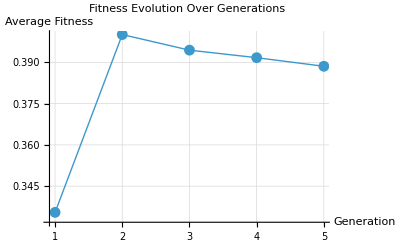

```mathematica
ListLinePlot[avgFitnessPerGen,PlotRange->All,Mesh->All,PlotStyle->Thick,AxesLabel->{"Generation","Average Fitness"},PlotLabel->"Fitness Evolution Over Generations",GridLines->Automatic]
```

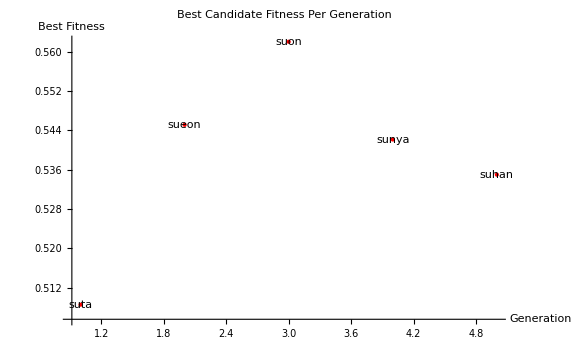

```mathematica
bestPerGenPlot=ListPlot[Table[{gen,fitnessFunction[allBest[[gen]]]},{gen,Length[allBest]}],PlotStyle->{Red,PointSize[Medium]},PlotRange->All,AxesLabel->{"Generation","Best Fitness"},Epilog->Table[Text[Style[allBest[[gen]],Medium],{gen,fitnessFunction[allBest[[gen]]]}+{0,0}],{gen,Length[allBest]}],PlotLabel->"Best Candidate Fitness Per Generation",ImageSize->Large]
```

Overall, there is a trend of increasing fitness throughout the graph. There are many fluctuations due to rando

## String Optimization

Linguistic evolution can also be viewed as an optimization problem. I want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. I take a string and evolve it through several hundred generations. Each generation, I evolve the string towards the multilingual word that is most different from it.

Set up basic variables:

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5];
startingWord = baseWord;
testList=translatedList
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=1000;
averageLength=Round[Mean[StringLength /@ testList]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars
];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},
maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}
];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

layoutTestWords[baseWord_, testList_] := 
  Module[{angles, positions}, 
   angles = Subdivide[0, 2*Pi, Length[testList]][[1 ;; -2]];
   positions = Table[
     With[{dist = EditDistance[baseWord, testList[[i]]]},
      {testList[[i]], 
       Cos[angles[[i]]]*dist, 
       Sin[angles[[i]]]*dist}
      ], {i, 1, Length[testList]}];
   positions];
```

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity,suraja,slonce,suran,taiyang,sonce,panonpoe,anwu,ilanga,aftab,araw,soare,zon,qorrax,son,adlaw}

I assign a weight to each character based on its frequency. This way, I encourage evolving towards more frequent characters at any position.

Calculate character frequencies for each position:

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables
]
```

Normalize frequencies to a decimal number between 0 and 1:

```mathematica
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[
total==0,
freqTable,
Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]
]
]
```

Calculate weighted character frequencies:

```mathematica
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
```

Decide the character to evolve into based on the frequency weightings:

```mathematica
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];
```

Mutate a character at randomly 5% of the time:

```mathematica
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
```

Evolve towards the decided character:

```mathematica
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];
```

Simulate hundreds of generations:

```mathematica
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=
Module[{target,newWord,newDist},
target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList
];
If[
newDist<bestDist,
{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},
{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}
]
];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];


testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

Generate animation:

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty},
currentWord=baseWordStates[[frame]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.003],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation


bestWord=StringReplace[bestWord,"_"->""];
Print["Best word found: ",bestWord];
Print["Best average distance: ",N[bestDistance]];
```

Best word found: sana

Best average distance: 4.

Plot the average word distance between the evolving string and multilingual word list over generations:

```mathematica
plotEvolutionProgress[baseWordStates_,testList_]:=Module[{distances,generations},distances=Table[Mean[EditDistance[baseWordStates[[i]],#]&/@testList],{i,1,Length[baseWordStates]}];
generations=Range[0,Length[baseWordStates]-1];
ListLinePlot[MovingAverage[Transpose[{generations,distances}], 3],PlotLabel->"Average Distance to Multilingual Wordlist (lower is better)",AxesLabel->{"Generation","Average Distance"},PlotStyle->{Red,Thick},GridLines->Automatic, AspectRatio->1, ImageSize->{550, 550}]]
```

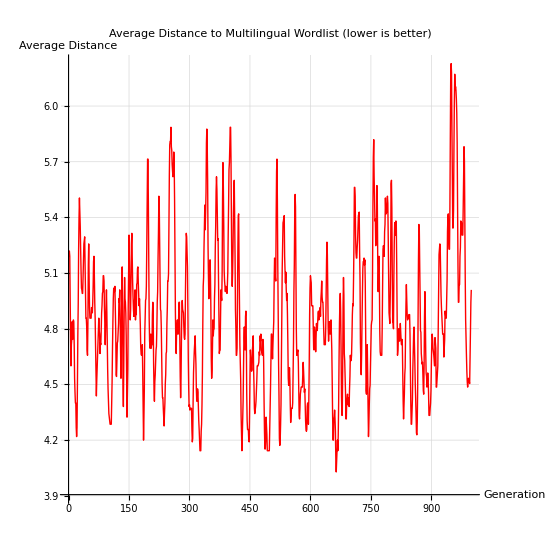

```mathematica
plotEvolutionProgress[baseWordStates, testList]
```

There is a weak decreasing trend in the average distance, showing a general improvement in evolution

## Generation with Morphological Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss",   MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1000  rounds:500  time:23s  examples/s:1394
data | ,,  training examples:35  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:5.92×10^-1  error:23.1%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{gune,qorr,ria,slon,sonn,sury}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords, bestWordGeneticPool, mostDigramGenerated,
     mostFreqCharWord, bestWord}]]
```

{gune,qorr,ria,slon,sonn,sury,suon,so,sourryya,sour,sourry,sonaa,sana}

## Generation with Phonetic Neural Net Features

I also apply the same neural net pipeline for multilingual words converted into the International Phonetic Alphabet (IPA).

Initialize the neural network:

```mathematica
netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

Because this network can only accept Roman letters, numerals, and punctuation, I map the IPA symbols to numbers and punctuation that is not contained .

Set up the mapping association:

```mathematica
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>
```

<|θ→1,ð→2,ʃ→3,ʒ→4,ɪ→5,ɛ→6,æ→7,ɔ→8,ʊ→9,ʌ→0,ə→.,ɜ→,,ŋ→;,ɡ→:,ɑ→!,ˈ→@,ˌ→=,ɒ→*,ɝ→[|>

```mathematica
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
```

```mathematica
convertedTrainList = StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList, "•"->""];
```

```mathematica
convertedTrainList
```

{suhn,s@9rj.,shamz,sol,sohlahl,s9r@j!,s.9l@ne,m7t.@h!ri,s@wrd4,son,r@a5,joouh,n9r@judu,uhnz,k.@t5r!v.n,t@e5j7;,ranuh,s@r6;5;:e,sohl,f@r7ks.15ti,s9@r!d4.,sl*ns,s9@r7n,t@a5j7;,s@0ns,p7n.n@po9,7;@wu,5@l!;.,7f@t7b,utput@!r.w,s@8r,zawn,k8@r!,suhn,7d@l8}

```mathematica
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
```

```mathematica
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
resultsPhon = 
 NetTrain[netPhon, <|"Input" -> convertedTrainList|>, All, LossFunction -> "Loss",  MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1000  rounds:500  time:25s  examples/s:1308
data | ,,  training examples:35  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:5.24×10^-1  error:18.7%
 | 
 | ]

```mathematica
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}]
```

NetChain[<3>]

```mathematica
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse /@ Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]], convertedTrainList]
```

{æŋˈw,joou,kɔˈr,ranu,sˈʌn,sˈʊr,sʊˈr}

```mathematica
extractorPhon=NetChain[{trainednetPhon,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
newAvgWordsPhonetics
```

{æŋˈw,joou,kɔˈr,ranu,sˈʌn,sˈʊr,sʊˈr}

## Graphical Interface

```mathematica
DynamicModule[{keyWord="sun",mostFreqCharWord="",mostDigramGenerated={},SYLLABLECOUNT=0,bestWordGeneticPool="",bestWord="",newAvgWords={}},Panel[Column[{Style["μLang Lexicon Generator",Bold,14],Row[{"Enter keyword: ",InputField[Dynamic[keyWord],String]}],Button["Generate",Module[{languages,rawTranslations,translatedList,charLists,avgLen,augmentedLists,transposed,mostFreqChar,positionedDigrams,groupedByPosition,countsByPosition,topDigramsByPosition,generateWord,populationSize,generations,mutationRate,fitnessFunction,population,randomString,allBest,words,charSet,MAXLENGTH,allPopulations,avgFitnessPerGen,phoneticDifference,bestCandidate,fitnesses,parents,baseWord,testList,padChar,baseWordStates,targetWords,GENERATIONS,averageLength,allPossibleChars,rawFrequencies,charFreqWeights,initialState,evolutionResults,finalWord,bestDistance,testPositions,positionDict,net,vocabulary,results,trainednet,generator,wordz},languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
rawTranslations=KeyValueMap[#1->First[#2]&,WordTranslation[keyWord,languages]];
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]],"notavailable"];


charLists=Characters/@translatedList;
avgLen=Round[Mean[Length/@charLists]];
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
transposed=Transpose[augmentedLists];
mostFreqChar=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,transposed];
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]];


positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}];
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables=RandomInteger[{Max[1,SYLLABLECOUNT-2],Min[Length[topDigramsByPosition],SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]];
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{7}]];


populationSize=100;
generations=5;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
allBest={};
words=translatedList;
charSet=Flatten[topDigramsByPosition];
MAXLENGTH=Round[Mean[StringLength/@words]];
allPopulations={};
avgFitnessPerGen={};
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];
fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore];
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
AppendTo[avgFitnessPerGen,N[Mean[fitnesses]]];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}];
AppendTo[allPopulations,population];
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];


baseWord=StringJoin@RandomChoice[CharacterRange["a","z"],5];
testList=translatedList;
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=1000;
averageLength=Round[Mean[StringLength/@testList]];
getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];
pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];
mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];
findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs];
layoutTestWords[baseWord_,testList_]:=Module[{angles,positions},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions=Table[With[{dist=EditDistance[baseWord,testList[[i]]]},{testList[[i]],Cos[angles[[i]]]*dist,Sin[angles[[i]]]*dist}],{i,1,Length[testList]}];
positions];
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];
charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,RandomChoice[list],weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]];
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight,chars,weights,choice},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=If[i<=Length[charFreqWeights],chars=Keys[charFreqWeights[[i]]];
weights=Values[charFreqWeights[[i]]];
choice=RandomChoice[weights->chars];
StringReplacePart[basePadded,choice,{i,i}],basePadded]]];
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=Module[{target,newWord,newDist},target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList];
If[newDist<bestDist,{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}]];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];
testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
bestWord=StringReplace[bestWord,"_"->""];


net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]];
results=NetTrain[net,<|"Input"->translatedList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList];

netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>;
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
convertedTrainList=StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList,"•"->""];
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]];
resultsPhon=NetTrain[netPhon,<|"Input"->convertedTrainList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}];
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse/@Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]],convertedTrainList];

],Method->"Queued"],Dynamic[If[mostFreqCharWord==="","",Panel[Column[{Row[{"Most frequent character word: ",Style[mostFreqCharWord,Blue,Bold]}],Row[{"Generated digram-based words: ",Style[Row[Riffle[mostDigramGenerated,", "]],Darker@Green]}],Row[{"Best word (genetic algorithm): ",Style[bestWordGeneticPool,Darker@Red,Bold]}],Row[{"Best word (evolution algorithm): ",Style[bestWord,Purple,Bold]}],Row[{"Neural network generated words: ",Style[Row[Riffle[newAvgWords,", "]],Orange,Bold]}],Row[{"Neural network phonetic words: ",Style[Row[Riffle[newAvgWordsPhonetics,", "]],RGBColor[0.6,0.2,0.8],Bold]}]}]]]]}]]]
```

## N-gram Evaluation

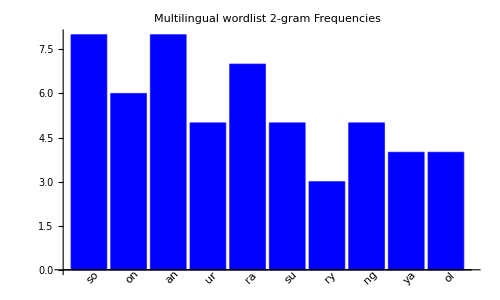

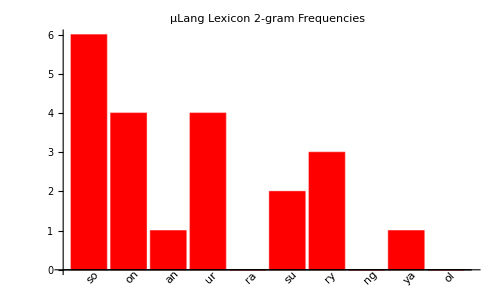

2-gram Frequencies

N-gram | List 1 Count | List 2 Count
so | 8 | 6
on | 6 | 4
an | 8 | 1
ur | 5 | 4
ra | 7 | 0
su | 5 | 2
ry | 3 | 3
ng | 5 | 0
ya | 4 | 1
ol | 4 | 0

3-gram Frequencies

N-gram | List 1 Count | List 2 Count
son | 3 | 2
sur | 4 | 1
sol | 4 | 0
ury | 3 | 1
ang | 3 | 0
nce | 3 | 0
our | 0 | 3
sou | 0 | 3
ana | 1 | 1
eng | 2 | 0

Statistical Summary (2-grams):

Metric | Value
TotalUniqueNgrams | 92
List1OnlyNgrams | 68
List2OnlyNgrams | 5
SharedNgrams | 19
JaccardSimilarity | 0.206522

Statistical Summary (3-grams):

Metric | Value
TotalUniqueNgrams | 108
List1OnlyNgrams | 85
List2OnlyNgrams | 10
SharedNgrams | 13
JaccardSimilarity | 0.12037

```mathematica
l1=translatedList;
l2=allPossibleWords;
topK=10;
ngramComparison[list1_,list2_,n_:2]:=Module[{ngrams1,ngrams2,freq1,freq2,allNgrams,combinedData},
ngrams1=Flatten[StringPartition[#,n,1]&/@list1];
ngrams2=Flatten[StringPartition[#,n,1]&/@list2];
freq1=Counts[ngrams1];
freq2=Counts[ngrams2];
allNgrams=Union[Keys[freq1],Keys[freq2]];
combinedData=Table[{ngram,Lookup[freq1,ngram,0],Lookup[freq2,ngram,0]},{ngram,allNgrams}];
combinedData=SortBy[combinedData,-Total[#[[2;;3]]]&];
Return[combinedData];
];


data=ngramComparison[l1, l2,2];
topData=Take[data,Min[topK,Length[data]]];

chart1=BarChart[#[[2]]&/@topData,ChartLabels->Placed[#[[1]]&/@topData,Below,Rotate[#,Pi/4]&],ChartStyle->Blue,PlotLabel->"Multilingual wordlist 2-gram Frequencies",ImageSize->500,AspectRatio->0.6]
chart2=BarChart[#[[3]]&/@topData,ChartLabels->Placed[#[[1]]&/@topData,Below,Rotate[#,Pi/4]&],ChartStyle->Red,PlotLabel->"μLang Lexicon 2-gram Frequencies",ImageSize->500,AspectRatio->0.6]
(*BarChart[Transpose[{#[[2]],#[[3]]}&/@topData],ChartLabels->Placed[#[[1]]&/@topData,Below,Rotate[#,Pi/4]&],ChartStyle->{Blue,Red},ChartLegends->{"Wordlist","Generated μLang lexicon"},PlotLabel->"N-gram Frequencies Comparison",ImageSize->500,AspectRatio->0.6]*)

"2-gram Frequencies"
ngram2Data=ngramComparison[l1, l2,2];
Print[TableForm[Take[ngram2Data,10],TableHeadings->{None,{"N-gram","List 1 Count","List 2 Count"}}]];

"3-gram Frequencies"
ngram3Data=ngramComparison[l1, l2,3];
Print[TableForm[Take[ngram3Data,10],TableHeadings->{None,{"N-gram","List 1 Count","List 2 Count"}}]];

ngramSimilarity[list1_,list2_,n_:2]:=Module[{ngrams1,ngrams2,intersection,union},ngrams1=Flatten[StringPartition[#,n,1]&/@list1];
ngrams2=Flatten[StringPartition[#,n,1]&/@list2];
intersection=Length[Intersection[ngrams1,ngrams2]];
union=Length[Union[ngrams1,ngrams2]];
Return[N[intersection/union]]; 
];

ngramStatistics[list1_,list2_,n_:2]:=Module[{data,stats},data=ngramComparison[list1,list2,n];
stats=Association["TotalUniqueNgrams"->Length[data],"List1OnlyNgrams"->Count[data,{_,x_,0}/;x>0],"List2OnlyNgrams"->Count[data,{_,0,x_}/;x>0],"SharedNgrams"->Count[data,{_,x_,y_}/;x>0&&y>0],"JaccardSimilarity"->ngramSimilarity[list1,list2,n]];
Return[stats];];

Print["\nStatistical Summary (2-grams):"];
stats=ngramStatistics[l1, l2,2];
Print[TableForm[{#,stats[#]}&/@Keys[stats],TableHeadings->{None,{"Metric","Value"}}]];

Print["\nStatistical Summary (3-grams):"];
stats=ngramStatistics[l1, l2,3];
Print[TableForm[{#,stats[#]}&/@Keys[stats],TableHeadings->{None,{"Metric","Value"}}]];

(*
jaccard sim.
size of the intersection divided by the size of the union of A, B
*)
```

```mathematica
(*FeatureSpacePlot[Join[Style[#,Blue,14]&/@(mfccTx), Style[#,Red,14]&/@(mfccAx)],LabelingSize->20,Axes->True,Method->"TSNE",ImageSize->{800,800},AspectRatio->1]*)
```

```mathematica
extractor=NetChain[{NetModel["Whisper-V1 Multilingual Nets"],AggregationLayer[Max,1]}][AudioPartition[#,30][[1]]]&;
FeatureSpacePlot[Join[Style[#,Blue,14]&/@(tx), Style[#,Red,14]&/@(ax)],FeatureExtractor->extractor,Axes->True,LabelingSize->20, AspectRatio->1]
```

DimensionReduction::mlbddata: The data is not formatted correctly.

FeatureSpacePlot[Join[tx,ax],FeatureExtractor→(NetChain[{NetModel[Whisper-V1 Multilingual Nets],AggregationLayer[Max,1]}][AudioPartition[#1,30]⟦1⟧]&),Axes→True,LabelingSize→20,AspectRatio→1]

## Ease of pronunciation

Now that we have a list of possibly generated words from our different methods,

```mathematica
allPossibleWords
```

{gune,qorr,ria,slon,sonn,sury,suon,so,sourryya,sour,sourry,sonaa,sana}

```mathematica
pronounceabilityScore[str_String]:=Module[{knownWords,syllables,vowelCount,consonantCount,vowelConsonantPenalty,dictionaryMatch,rareClusterPenalty,normalizedLength,totalScore},rareClusterPenalty=StringCount[str,RegularExpression["[^aeiouyAEIOUY]{3,}"]];
If[rareClusterPenalty>0,Return[1000]];
knownWords=DictionaryLookup["*"];
syllables=StringCount[ToLowerCase[str],RegularExpression["[aeiouy]+"]];
dictionaryMatch=Min[EditDistance[ToLowerCase[str],#]&/@Select[knownWords,Abs[StringLength[#]-StringLength[str]]<=2&]];
normalizedLength=StringLength[str]/10.0;
vowelCount=StringCount[str,RegularExpression["[aeiouyAEIOUY]"]];
consonantCount=StringLength[str]-vowelCount;
vowelConsonantPenalty=Abs[vowelCount-consonantCount]/StringLength[str];
totalScore=syllables+dictionaryMatch/10+vowelConsonantPenalty+normalizedLength;
totalScore;
]
```

```mathematica
pronounceabilityScore[#]&/@allPossibleWords;
sortedByPronunciation = Reverse[SortBy[allPossibleWords,pronounceabilityScore]];
sortedByPronunciation
```

{sury,suon,sourryya,sourry,sour,sonn,sonaa,so,slon,sana,ria,qorr,gune}

## Swadesh

```mathematica
ResourceObject["Swadesh Lists"]
```

ResourceObject[…]

```mathematica
x=ResourceData["Swadesh Lists"];
```